# Performance on Trotter vs recompilation

Note: Use mathematica 12, mathematica 13 is buggy in the pattern part

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
```

```mathematica
Import["https://qtechtheory.org/questlink.m"];
SetDirectory[NotebookDirectory[]];
CreateLocalQuESTEnv["quest_link_cpu"];
```

## Modules

### Some helpers

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit;daniel's format";
FormatHamiltonian[filename_,total_:False]:=Module[{stringham,ham,nterms,nqubits},
stringham=Import[filename];
ham=ToExpression[stringham];
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
nterms=Length@ham;
If[total,
{Total@Apply[Times,ham,1],nterms,nqubits}
,
{ham,nterms,nqubits}
]
]

GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]

CountGates::usage="CountGates[circuit], return the count for {cnots, singles}";
CountGates[circuit_]:=Module[{cnotc},
cnotc=Count[circuit/.{Subscript[C, _][_]->2,Subscript[_, _]-> 1,Subscript[_, _][_]->1},2];
{cnotc,Length@circuit-cnotc}
]

SetAttributes[MergeGates,HoldFirst]
MergeGates::usage="MergeGates[circuits], simplify circuits.";
MergeGates[circuits_]:=Module[{circc,circs,len,a,b,c,d,e,f,θ,j,i},
circs=Flatten@circuits;
While[True,
len=Length@circs;
circc=GetCircuitColumns[circuits];
circc=circc//.{
{a___,{b___,Subscript[H, j_],c___},{d___,Subscript[H, j_],e___},f___}->{a,{b,c},{d,e},f},
{a___,{b___,Subscript[Rx, j_][θ_],c___},{d___,Subscript[Rx, j_][-θ_],e___},f___}->{a,{b,c},{d,e},f},
{a___,{b___,Subscript[Rx, j_][-θ_],c___},{d___,Subscript[Rx, j_][θ],e___},f___}->{a,{b,c},{d,e},f},
{a___,{b___,Subscript[Rx, j_][θ_],c___},{d___,Subscript[Rx, j_][θ_],e___},f___}->{a,{b,Subscript[Rx, j][2θ],c},{d,e},f},
{a___,{b___,Subscript[C, j_][Subscript[X, i_]],c___},{d___,Subscript[C, j_][Subscript[X, i_]],e___},f___}->{a,{b,c},{d,e},f}
};
circs=Flatten@circc;
If[Length@circs===len,
Break[]]
];
circs
]

MatrixDist::usage="MatrixDist[matrix1, matrix2, subspace, plotglobalphase:False]. Calculate distance of 2 matrices by formula: 
                                    max_λ |Π_S(U-V)Π_S| 
                    namely, maximum absolute eigenvalues of the matrix difference projected to the subspace of interest.";
MatrixDist[M1_,M2_,subspace_,plotglobalphase_:False]:=Module[{sm1,sm2,globalphase,mindist,F,ϕ},
{sm1,sm2}=If[Length@subspace<Length@M1,{GetSubMatrix[M1,subspace],GetSubMatrix[M2,subspace]},{M1,M2}];
F[ϕ_?NumericQ]:=Max[Sqrt[Eigenvalues[GetSubMatrix[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2),subspace]]]];
{mindist,globalphase}=NMinimize[{F[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5];
If[plotglobalphase,Print@DiscretePlot[F[ϕ],{ϕ,0,2π,0.01},AxesLabel->{"ϕ","max_λ |Π_S(U-ⅇ^ⅈϕV)Π_S|"},PlotLabel->ToString@subspace]];
{mindist,ϕ/.globalphase}
]

GetSubMatrix::usage="GetSubMatrix[matrix,subspace]. Return the submatrix in the subspace.";
GetSubMatrix[matrix_,subspace_ ]:=Module[{sm,dim,x=0,y=0},
dim=Length@subspace;
sm=IdentityMatrix[dim];
Table[
++x;y=0;
Table[
++y;
sm⟦x,y⟧=matrix⟦s+1,ss+1⟧;
,{ss,subspace}]
,{s,subspace}];
sm
]
```

### Trotterization-related modules

Reference:
https://aip.scitation.org/doi/10.1063/1.4768229

```mathematica
PauliCirc::usage="PauliCirc[coefficient, pauli_list, nqubits, prefactor]. Return the circuit of a term.";
PauliCirc[coef_,paulis_,nqubits_,factor_:1]:=Module[{circ,p,q,ngates},
If[Length@paulis>0,
circ=Table[
{p,q}=Level[c,-1];
Which[p===Z,{Subscript[C, q][Subscript[X, nqubits]]},p===X,{Subscript[Ry, q][π/2],Subscript[C, q][Subscript[X, nqubits]],Subscript[Ry, q][-π/2]},p===Y,{Subscript[Rx, q][-π/2],Subscript[C, q][Subscript[X, nqubits]],Subscript[Rx, q][π/2]}]
,{c,paulis}];
Join[circ,{{Subscript[Rz, nqubits][coef*factor]}},Reverse@circ]
,
circ={}
]
]


Propagator::usage="Propagator[coefficient, pauli_list, nqubits, prefactor]. Return the circuit of a propagator.";
Propagator[coef_,paulis_,factor_]:=Module[{lpaulis,p,q,ngates,ops,ids,rops,ropsd,rcnot,j,i,pauliops},
rops={Subscript[X, j_]->Subscript[H, j], Subscript[Y, j_]->Subscript[Rx, j][-π/2], Subscript[Z, _]->{}};
ropsd={Subscript[X, j_]->Subscript[H, j], Subscript[Y, j_]->Subscript[Rx, j][π/2], Subscript[Z, _]->{}};
rcnot={{i_Integer,j_Integer}->Subscript[C, i][Subscript[X, j]] ,{{_Integer}}->{} };
lpaulis=Table[{p,q}=Level[c,-1],{c,paulis}];
lpaulis=SortBy[lpaulis,#⟦2⟧&];
{ops,ids}={lpaulis⟦All,1⟧,Partition[lpaulis⟦All,2⟧,2,1]};
If[Length@ids<1, ids={lpaulis⟦All,2⟧}];
pauliops=Subscript[#⟦1⟧, #⟦2⟧]&/@lpaulis;
Flatten@{pauliops/.rops,ids/.rcnot,Subscript[Rz, Last@Last@ids][2*coef*factor],Reverse[ids/.rcnot],pauliops/.ropsd}
]


IsCommute::usage="IsCommute[List_paulis1, List_paulis2]. Return boolean indicates commutativity.";
IsCommute[P1_List,P2_List]:=Module[{m1,m2,nq,i},
nq=1+Max[Flatten@{P1,P2}/.Subscript[_, i_]->i];
m1=CalcCircuitMatrix[P1,nq];
m2=CalcCircuitMatrix[P2,nq];
If[Norm[m1.m2-m2.m1]≤10^-13,
True,
False]
]

PartitionPaulis::usage="ParititionPaulis[paulis], partition a list of pauli operators by commutation.";
PartitionPaulis[paulis_List]:=Module[{list1, list2},
list1={paulis⟦1⟧};list2={};
Table[
If[(AllTrue@@IsCommute[p⟦2;;⟧,#⟦2;;⟧]&/@list1)⟦1⟧,
AppendTo[list1,p],AppendTo[list2,p]]
,{p,paulis⟦2;;⟧}];
(*sanity checck*)
If[¬AllTrue[IsCommute[#⟦1⟧⟦2;;⟧,#⟦2⟧⟦2;;⟧]&/@Subsets[list1,{2}]],
Print["ERR: there is a non-commuting operation in set A"]];
If[¬AllTrue[IsCommute[#⟦1⟧⟦2;;⟧,#⟦2⟧⟦2;;⟧]&/@Subsets[list2,{2}]],
Print["ERR: there is a non-commuting operation in set B"]];
{list1,list2}
]

TrotterizeNaive::usage="TrotterizeNaive[hamiltonian_path, t, n]. Return the trotterization circuit, if full=False, it's not powered by n yet.";
TrotterizeNaive[hamfile_,t_,n_]:=Module[{ham,nqubits,nterms,r=N[t/n],estgates,esterr,circ},
{ham,nterms,nqubits}=FormatHamiltonian[hamfile,False];
ham=DeleteCases[ham,{_}]; (*delete the global phase*)
estgates=(2*Length@Flatten@ham-nterms)*n;
esterr=r^2//N;
circ=Flatten[Table[Propagator[paulis⟦1⟧,paulis⟦2;;⟧,r],{paulis,ham}],1];
Flatten@ConstantArray[circ,n]
]


Trotterize::usage="Trotterize[hamiltonian_path, t, n, order:1]. Return the trotterization circuit. Available up to the fourth order.
The paulis are partitioned into two sets A and B in which each element is commuting each other. 
Trotterization is available up to the 4th order
order 1: e^((A + B) t)=(e^(At/n)e^(Bt/n))^n+O(t Δt)
order 2: e^((A + B) t)=(e^(At/2  n)e^(Bt/n)e^(At/2  n))^n+O(t Δt^2)
order 2comp: is order 2 but compressed
order 2scb :(e^(At/2  n)e^(Bt/n)e^(At/2  n))(e^(Bt/2  n)e^(At/n)e^(Bt/2  n))(e^(At/2  n)e^(Bt/n)e^(At/2  n))
order 3: e^((A + B) t)=(e^(7/24)e^(2/3)e^(3/4)e^(-2/3)e^(-1/24)e^(Bt/n))^n+O(t Δt^3)
order 4: e^((A + B) t)=Π_(i = 1,  ... , 5)(e^p_ie^p_ie^p_i)^n+O(t Δt^4),where p1=p2=p4=p5=1/(4-4^(1/3)),p3=1-4p1
";
Trotterize[hamfile_,t_,n_,order_:1]:=Module[{ham,nterms,nqubits,list1,list2,Δt,f},
{ham,nterms,nqubits}=FormatHamiltonian[hamfile,False];
ham=DeleteCases[ham,{_}]; (*delete the global phase*)
{list1,list2}=PartitionPaulis[ham];
Which[
order===1,
f=N[t/n];
Flatten@Table[{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}]
},{n}]
,
order===2,
f=N[0.5*t/n];
Flatten@Table[{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}]
},{n}]
,
(*compressed2 -- check if it results in the circuit order 2
template: Flatten@{e^(A/2),e^B,Table[{e^A,e^B},{n-1}],e^(A/2)}
*)
order ==="2comp",
f=N[0.5*t/n];
Flatten@{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}],
Table[{Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list1}],Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}]},{n-1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}]
}
,
(*simon's version of order 2*)
order==="2scb",
f=N[0.5*t/n];
Flatten@Table[
If[OddQ@iter,
{Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}]}
,
{Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}]}]
,{iter,n}] (*fucking weird bug, using "i" instead of "iter" will mess up indices; I guess because I used "i" in Propagator function, but wtf? *)
,
order===3,
f=N[t/n];
Flatten@Table[{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,(7/24)f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,(2/3)f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,(3/4)f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,((-2)/3)f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,((-1)/24)f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}]
},{n}]
,
order===4,
f=ConstantArray[N[1/(4-4^(1/3))],5];
f⟦3⟧=N[1-4f⟦1⟧];
f=(0.5*t/n)*f;
Flatten@Table[
Flatten[Flatten@{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,#],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2#],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,#],{p,list1}]
}&/@f]
,{n}]
]
]
```

## H_2 molecule

### Module specific to results

```mathematica
getSummary::usage="getSummary[circuit, hamiltonianMatrix, t, observedState(ground state)].
Returns {{twos-count,singles-count}, distance, ent fidelity, <e-e'>, 1-<ψ(t)|ψ'(t)>}"
getSummary[circ_,hammat_,t_,state_,subspace_:Null]:=Module[{dham,approxmat,singles,twos,dist,nqubits,space,nancilla,nconst,sbasis,entstate,entfid,eerr,fiderr,vec,vecapprox},
(*analytic matrix as reference *)
nqubits=Log2@Length@hammat;
dham=MatrixExp[-ⅈ t hammat]//Chop;
approxmat=CalcCircuitMatrix[circ,nqubits];
space=If[subspace===Null,Range[0,2^nqubits-1],subspace];

(*gates count*)
{twos,singles}=CountGates[circ];
(*distance*)
dist=MatrixDist[dham,approxmat,space];
(*entanglement infidelity*)
nancilla=Max[Ceiling[Log2[Length@subspace]],1];
sbasis=Table[subspace⟦idx+1⟧+2^nqubits*idx,{idx,0,Length@subspace-1}];
entstate=ConstantArray[0.,2^(nqubits+nancilla)];
Table[entstate⟦k+1⟧=nconst,{k,sbasis}];
entfid=1-Abs[entstate.KroneckerProduct[Inverse[approxmat].dham,IdentityMatrix[2^nancilla]].entstate]^2;
(*expected energy*)
vec=dham.state;
vecapprox=approxmat.state;
eerr=Conjugate[vecapprox].hammat.vecapprox-Conjugate[vec].hammat.vec;
(*infidelity to the true evolution state*)
fiderr=1-Abs[Conjugate[vec].vecapprox]^2;
{{twos,singles},First@dist,entfid,Re@eerr,fiderr}
]
```

getSummary[circuit, hamiltonianMatrix, t, observedState(ground state)].
Returns {{twos-count,singles-count}, distance, ent fidelity, <e-e'>, 1-<ψ(t)|ψ'(t)>}

```mathematica
ClearAll[PlotEErr]
PlotEErr[trotsum_,label_,opts_:{}]:=Module[{eerr,minval,n,idxdata},
n=Length@Keys@trotsum;
eerr=If[label===1,
Table[Table[Labeled[{i,trotsum[order][[i,4]]},Total@trotsum[order][[i,label]],Right],{i,Length@trotsum[1]}],{order,Keys@trotsum}],
Table[Table[Labeled[{i,trotsum[order][[i,4]]},NumberForm[trotsum[order][[i,label]],2],Top,FrameMargins->None,FrameStyle->Transparent,Spacings->{0, 0}],{i,Length@trotsum[1]}],{order,Keys@trotsum}]
];
minval=Min[(Join@@Values[trotsum])[[All,4]]];
ListLogPlot[eerr,LabelStyle->{FontFamily->"Asana Math",FontSize->15,Background->None},FrameLabel->{"Trotter number",TraditionalForm["ΔE"]},Frame->True,FrameStyle->{{Black,Black},{Black,Black}},PlotStyle->PointSize[Medium],PlotRange->{{0.5,2+n},{10^Floor[Log10@minval],1}},Background->White,GridLines->{None, {chemacc}},GridLinesStyle->Directive[Red, Dashed,Thick],PlotLegends->Placed[PointLegend[Automatic,( "order "<>ToString[#]&/@Range[4]),Spacings->0.1,LegendMarkerSize->5,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False)]&)],
{0.9,0.9}],opts]
]

PlotDists[trotsum_,opts_:{}]:=Module[{dists},
dists={#[[2]],#[[4]]}&/@(Join@@Values@trotsum);
ListLogLinearPlot[dists,LabelStyle->{FontFamily->"Serif",FontSize->10,Background->None},FrameLabel->{"matrix distance","ϵ_energy"},Frame->True,FrameStyle->{{Black,Black},{Black,Black}},PlotStyle->PointSize[Medium],PlotRange->Automatic,Background->White,GridLines->{None, {chemacc}},GridLinesStyle->Directive[Red, Dashed,Thick],opts]
]
```

```mathematica
Options@Labeled
```

{Alignment→{Center,Baseline},Background→None,BaselinePosition→Automatic,BaseStyle→{},ContentSize→Automatic,DefaultBaseStyle→Labeled,DefaultLabelStyle→LabeledLabel,Editable→Automatic,Frame→None,FrameMargins→0,FrameStyle→Automatic,ImageMargins→0,ImageSize→Automatic,LabelStyle→{},RotateLabel→False,RoundingRadius→0,Selectable→Automatic,Spacings→Automatic,SyntaxForm→Automatic}

### Plots on trotter

```mathematica
filepath="/home/cica/vqe/molecules/H2/H2.txt";
t=1;
{ham,nterms,nqubits}=FormatHamiltonian[filepath,True];
(*delete the global phase*)
hammat=CalcPauliSumMatrix[DeleteCases[ham,{_}]];
eigsys=Eigensystem[hammat];
(*groundstate vector*)
gsvec=First@eigsys[[2,Ordering[eigsys[[1]],1] ]];
```

```mathematica
times
```

{0.001,0.005,0.01,0.05,0.1,0.5,1,2,4}

```mathematica
orders={1,"2scb",3,4};
trotsum=<|
Table[
t->
<|Table[
Print["t=",t,"; order=",order];
order->
Table[getSummary[MergeGates[Trotterize[filepath,t,n,order]],hammat,t,gsvec],{n,5}],{order,orders}]|>
,{t,times}]|>;
```

t=0.001; order=1

t=0.001; order=2scb

t=0.001; order=3

t=0.001; order=4

t=0.005; order=1

t=0.005; order=2scb

t=0.005; order=3

t=0.005; order=4

t=0.01; order=1

t=0.01; order=2scb

t=0.01; order=3

t=0.01; order=4

t=0.05; order=1

t=0.05; order=2scb

t=0.05; order=3

t=0.05; order=4

t=0.1; order=1

t=0.1; order=2scb

t=0.1; order=3

t=0.1; order=4

t=0.5; order=1

t=0.5; order=2scb

t=0.5; order=3

t=0.5; order=4

t=1; order=1

t=1; order=2scb

t=1; order=3

t=1; order=4

t=2; order=1

t=2; order=2scb

t=2; order=3

t=2; order=4

t=4; order=1

t=4; order=2scb

t=4; order=3

t=4; order=4

```mathematica
DumpSave["trotsum.mx",trotsum];
```

```mathematica
trotsum<<trotsum.mx;
```

```mathematica
chemacc=1.59*10^-3;
```

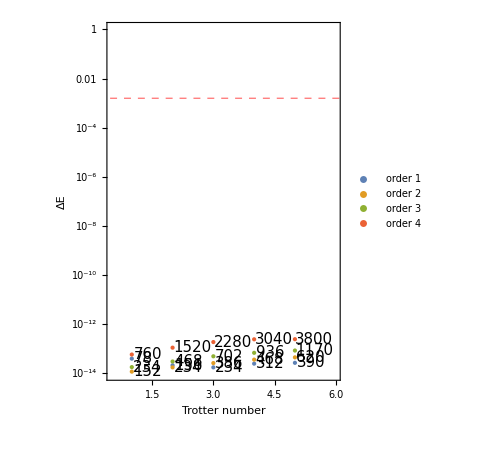
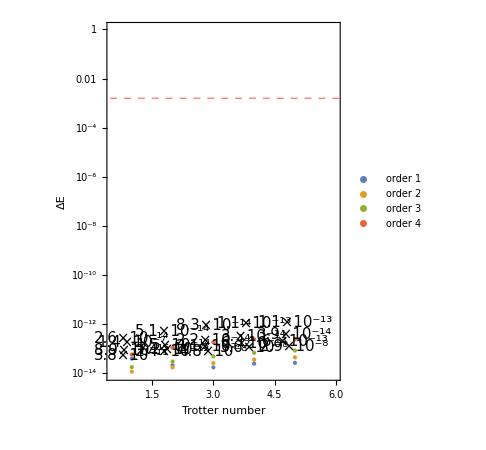
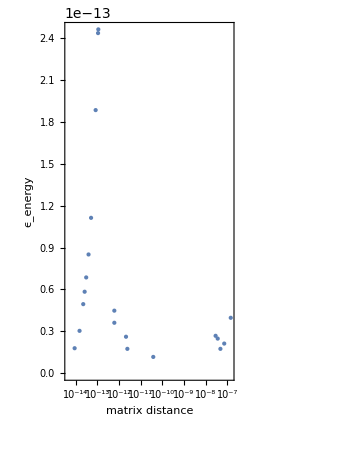

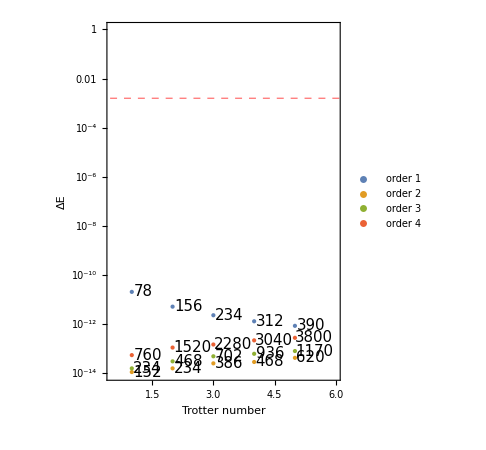
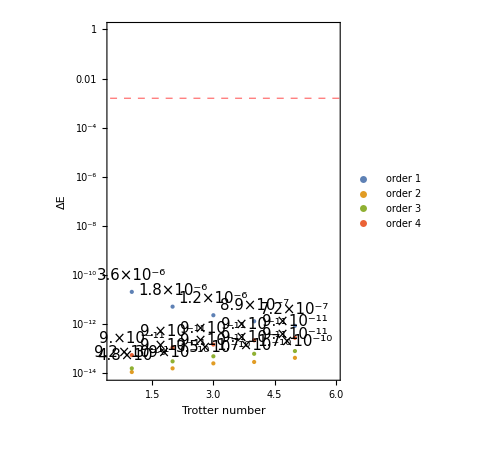
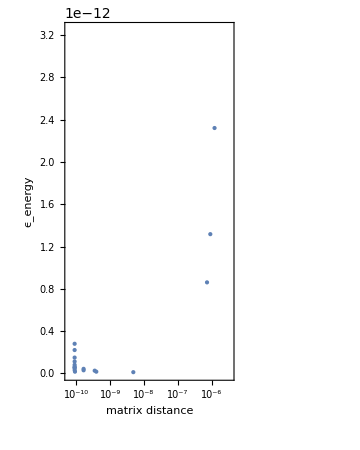

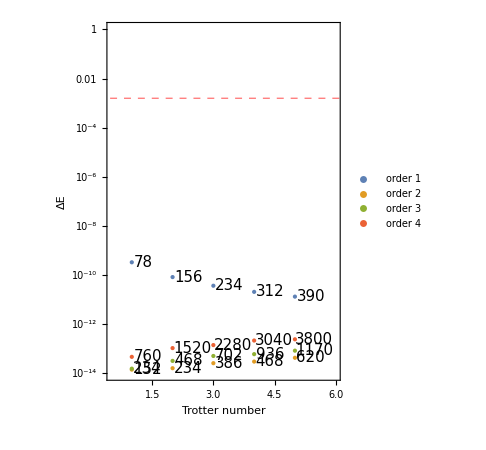
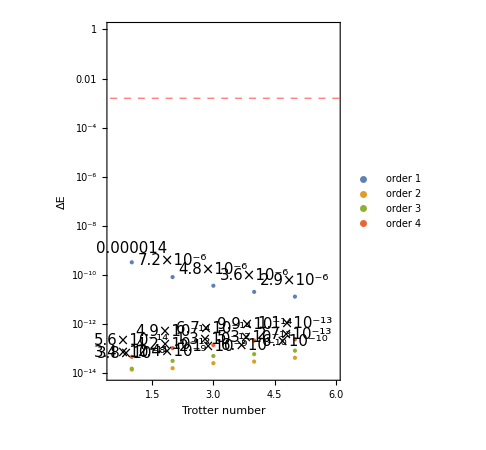

```mathematica
opt[t_]:={AspectRatio->5/4,ImageSize->Medium,Epilog->Text[Style["Δt="<>ToString[t],Medium]]}
Table[Print@Row@{PlotEErr[trotsum[t],1,opt[t]],PlotEErr[trotsum[t],2,opt[t]],PlotDists[trotsum[t],opt[t]]},{t,times}];
```

### Plots on recompilation

```mathematica
NotebookDirectory[]
```

/home/cica/chemistry-code/dynamics/

```mathematica
resfullH2<<resfullH2.mx;
```

```mathematica
?getSummary
```

```mathematica
getSummary[resfullH2[0.001][[1,5]],hammat,0.001,gsvec]
```

$Aborted

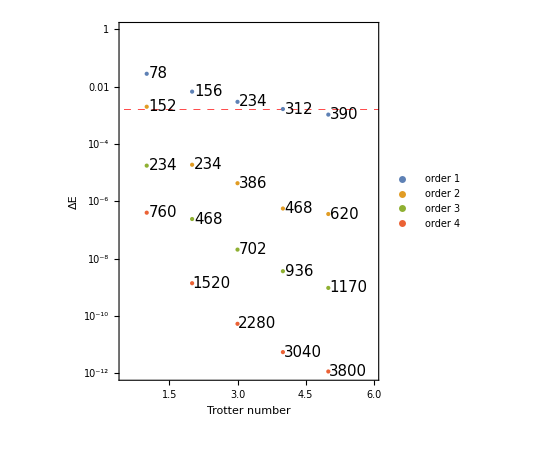
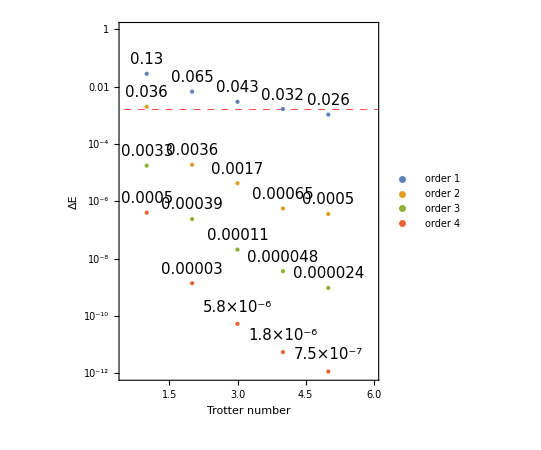

```mathematica
Row[
{PlotEErr[trotsum[1],1,{ImageSize->{400,450},AspectRatio->9/8,Ticks->{{1,2,3,4,5}, Automatic}}],
PlotEErr[trotsum[1],2,{ImageSize->{400,450},AspectRatio->9/8,Ticks->None}]}
]
```

```mathematica
Options@Labeled
```

{Alignment→{Center,Baseline},Background→None,BaselinePosition→Automatic,BaseStyle→{},ContentSize→Automatic,DefaultBaseStyle→Labeled,DefaultLabelStyle→LabeledLabel,Editable→Automatic,Frame→None,FrameMargins→0,FrameStyle→Automatic,ImageMargins→0,ImageSize→Automatic,LabelStyle→{},RotateLabel→False,RoundingRadius→0,Selectable→Automatic,Spacings→Automatic,SyntaxForm→Automatic}

## Other stuff

```mathematica
trotres={Trotterize[filepath,t,#,1],Trotterize[filepath,t,#,2],Trotterize[filepath,t,#,"2comp"],Trotterize[filepath,t,#,"2scb"],Trotterize[filepath,t,#,3],Trotterize[filepath,t,#,4]}&/@Range[n];
trotres2=Map[MergeGates,trotres,{2}];
```

```mathematica
header={"n","order 1","order 2","order 2comp","order 2scb", "order 3", "order 4"};
counts=Map[CountGates,trotres2,{2}];
dists=Map[MatrixDist[dham,CalcCircuitMatrix[#,nqubits]//Chop,Range[0,2^nqubits-1]]&,trotres2,{2}]
```

{{{0.132971,0.0970663},{0.035515,0.0970663},{0.035515,0.0970663},{0.035515,0.0970663},{0.00333144,0.0970663},{0.000503347,0.0970663}},{{0.0645773,0.0970663},{0.00858252,0.0970663},{0.00858252,0.0970663},{0.00359432,0.0970663},{0.000387835,0.0970663},{0.0000297521,0.0970663}},{{0.0428271,0.0970663},{0.00379109,0.0970663},{0.00379109,0.0970663},{0.00169678,0.0970663},{0.000113377,0.0970663},{5.81943×10^-6,0.0970663}},{{0.032062,0.0970663},{0.00212793,0.0970663},{0.00212793,0.0970663},{0.000647037,0.0970663},{0.000047605,0.0970663},{1.83499×10^-6,0.0970663}},{{0.0256281,0.0970663},{0.00136053,0.0970663},{0.00136053,0.0970663},{0.000502289,0.0970663},{0.0000243203,0.0970663},{7.50428×10^-7,0.0970663}}}

```mathematica
Print@TableForm@{{"Number gates in trotterization","Number gates in trotterization after merging"},
{TextGrid[Join[{header},ArrayFlatten[{{Transpose[{Range@n}],Map[Length,trotres,{2}]}}]],Frame->All],
TextGrid[Join[{header},ArrayFlatten[{{Transpose[{Range@n}],Map[Length,trotres2,{2}]}}]],Frame->All]}
};
Print@"Merged gates";
Print@TableForm@{{"CNOTs","Singles"},
{TextGrid[Join[{header},ArrayFlatten[{{Transpose[{Range@n}],Map[First,counts,{2}]}}]],Frame->All],
TextGrid[Join[{header},ArrayFlatten[{{Transpose[{Range@n}],Map[Last,counts,{2}]}}]],Frame->All]}
};
Print@"Matrix distance";
Print@TextGrid[Join[{header},ArrayFlatten[{{Transpose[{Range@n}],Map[First,dists,{2}]}}]],Frame->All];
```

Number gates in trotterization | Number gates in trotterization after merging
n | order 1 | order 2 | order 2comp | order 2scb | order 3 | order 4
1 | 82 | 160 | 160 | 160 | 246 | 800
2 | 164 | 320 | 242 | 246 | 492 | 1600
3 | 246 | 480 | 324 | 406 | 738 | 2400
4 | 328 | 640 | 406 | 492 | 984 | 3200
5 | 410 | 800 | 488 | 652 | 1230 | 4000 | n | order 1 | order 2 | order 2comp | order 2scb | order 3 | order 4
1 | 78 | 152 | 152 | 152 | 234 | 760
2 | 156 | 304 | 230 | 234 | 468 | 1520
3 | 234 | 456 | 308 | 386 | 702 | 2280
4 | 312 | 608 | 386 | 468 | 936 | 3040
5 | 390 | 760 | 464 | 620 | 1170 | 3800

Merged gates

CNOTs | Singles
n | order 1 | order 2 | order 2comp | order 2scb | order 3 | order 4
1 | 36 | 72 | 72 | 72 | 108 | 360
2 | 72 | 144 | 108 | 108 | 216 | 720
3 | 108 | 216 | 144 | 180 | 324 | 1080
4 | 144 | 288 | 180 | 216 | 432 | 1440
5 | 180 | 360 | 216 | 288 | 540 | 1800 | n | order 1 | order 2 | order 2comp | order 2scb | order 3 | order 4
1 | 42 | 80 | 80 | 80 | 126 | 400
2 | 84 | 160 | 122 | 126 | 252 | 800
3 | 126 | 240 | 164 | 206 | 378 | 1200
4 | 168 | 320 | 206 | 252 | 504 | 1600
5 | 210 | 400 | 248 | 332 | 630 | 2000

Matrix distance

n | order 1 | order 2 | order 2comp | order 2scb | order 3 | order 4
1 | 0.132971 | 0.035515 | 0.035515 | 0.035515 | 0.00333144 | 0.000503347
2 | 0.0645773 | 0.00858252 | 0.00858252 | 0.00359432 | 0.000387835 | 0.0000297521
3 | 0.0428271 | 0.00379109 | 0.00379109 | 0.00169678 | 0.000113377 | 5.81943×10^-6
4 | 0.032062 | 0.00212793 | 0.00212793 | 0.000647037 | 0.000047605 | 1.83499×10^-6
5 | 0.0256281 | 0.00136053 | 0.00136053 | 0.000502289 | 0.0000243203 | 7.50428×10^-7

```mathematica
t=0.9;
dham=MatrixExp[-ⅈ t CalcPauliSumMatrix[ham]]//Chop;
```

```mathematica
n=1;
trotres={Trotterize[filepath,t,#,1],Trotterize[filepath,t,#,2],Trotterize[filepath,t,#,"2comp"],Trotterize[filepath,t,#,"2scb"],Trotterize[filepath,t,#,3],Trotterize[filepath,t,#,4]}&/@Range[n];
trotres2=Map[MergeGates,trotres,{2}];
header={"n","order 1","order 2","order 2comp","order 2scb", "order 3", "order 4"};
counts=Map[CountGates,trotres2,{2}];
dists=Map[MatrixDist[dham,CalcCircuitMatrix[#,nqubits]//Chop,Range[0,2^nqubits-1]]&,trotres2,{2}]
Print@TableForm@{{"Number gates in trotterization","Number gates in trotterization after merging"},
{TextGrid[Join[{header},ArrayFlatten[{{Transpose[{Range@n}],Map[Length,trotres,{2}]}}]],Frame->All],
TextGrid[Join[{header},ArrayFlatten[{{Transpose[{Range@n}],Map[Length,trotres2,{2}]}}]],Frame->All]}};
Print@"Merged gates";
Print@TableForm@{{"CNOTs","Singles"},
{TextGrid[Join[{header},ArrayFlatten[{{Transpose[{Range@n}],Map[First,counts,{2}]}}]],Frame->All],
TextGrid[Join[{header},ArrayFlatten[{{Transpose[{Range@n}],Map[Last,counts,{2}]}}]],Frame->All]}};
Print@"Matrix distance";
Print@TextGrid[Join[{header},ArrayFlatten[{{Transpose[{Range@n}],Map[First,dists,{2}]}}]],Frame->All];
```

{{{0.109227,0.0873596},{0.0262165,0.0873596},{0.0262165,0.0873596},{0.0262165,0.0873596},{0.00219344,0.0873596},{0.000299216,0.0873596}}}

Number gates in trotterization | Number gates in trotterization after merging
n | order 1 | order 2 | order 2comp | order 2scb | order 3 | order 4
1 | 82 | 160 | 160 | 160 | 246 | 800 | n | order 1 | order 2 | order 2comp | order 2scb | order 3 | order 4
1 | 78 | 152 | 152 | 152 | 234 | 760

Merged gates

CNOTs | Singles
n | order 1 | order 2 | order 2comp | order 2scb | order 3 | order 4
1 | 36 | 72 | 72 | 72 | 108 | 360 | n | order 1 | order 2 | order 2comp | order 2scb | order 3 | order 4
1 | 42 | 80 | 80 | 80 | 126 | 400

Matrix distance

n | order 1 | order 2 | order 2comp | order 2scb | order 3 | order 4
1 | 0.109227 | 0.0262165 | 0.0262165 | 0.0262165 | 0.00219344 | 0.000299216

### Over different time

```mathematica
filepath="~/vqe/molecules/H2/H2.txt";
{ham,nterms,nqubits}=FormatHamiltonian[filepath,True];
(*delete the global phase*)
ham=DeleteCases[ham,{_}];
hammat=CalcPauliSumMatrix[ham];
```

```mathematica
eigs=Eigensystem@hammat;
```

```mathematica
gsvec=eigs[[2]][[1]]
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.993647+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.112544+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
v1=dham.gsvec
v2=trotmat.gsvec
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.987228-0.112762 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.111817+0.0127719 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.581244-0.789806 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.175132+0.0876949 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
e1=Conjugate[v1].hammat.v1//Chop
e2=Conjugate[v2].hammat.v2//Chop
```

-1.13728

-1.11817

```mathematica
e2-e1
```

0.0191174

```mathematica
time=Array[#&,10,{0.1,1}]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
dham=MatrixExp[-ⅈ 0.1 hammat]//Chop;
trotcirc=MergeGates@Trotterize[filepath,t,1,1];
trotmat=CalcCircuitMatrix@trotcirc//Chop;
```

```mathematica
eigv=Eigenvalues@dham;
eigt=Eigenvalues@trotmat;
```

```mathematica
eigv
```

{0.998833-0.0482955 ⅈ,0.998592+0.0530524 ⅈ,0.999007+0.0445468 ⅈ,0.999007+0.0445468 ⅈ,0.999858+0.0168344 ⅈ,0.995742-0.0921868 ⅈ,0.997444-0.0714495 ⅈ,0.999368-0.0355446 ⅈ,0.999368-0.0355446 ⅈ,0.999712-0.0240012 ⅈ,0.999712-0.0240012 ⅈ,0.99354+0.113483 ⅈ,0.998552+0.0537946 ⅈ,0.998552+0.0537946 ⅈ,0.998592+0.0530524 ⅈ,0.998592+0.0530524 ⅈ}

```mathematica
eigt
```

{0.9512+0.308575 ⅈ,0.997943+0.0641135 ⅈ,0.924781+0.3805 ⅈ,0.868317-0.496009 ⅈ,0.954329-0.298759 ⅈ,0.595423+0.803413 ⅈ,0.922215+0.386677 ⅈ,0.922215+0.386677 ⅈ,0.924781+0.3805 ⅈ,0.924781+0.3805 ⅈ,0.9512+0.308575 ⅈ,0.954329-0.298759 ⅈ,0.744538-0.66758 ⅈ,0.607235-0.794523 ⅈ,0.918183-0.396158 ⅈ,0.918183-0.396158 ⅈ}

```mathematica
resfulltrot=<||>;
ressubtrot=<||>;
lentrot=<||>;
Table[
resfulltrot[t]={};
ressubtrot[t]={};
lentrot[t]={};
Table[
dham=MatrixExp[-ⅈ t CalcPauliSumMatrix[ham]]//Chop;
trotcirc=MergeGates@Trotterize[filepath,t,1,order];
mat=CalcCircuitMatrix@trotcirc//Chop;
AppendTo[lentrot[t],Length@trotcirc];
AppendTo[resfulltrot[t],MatrixDist[dham,mat,Range[Length@dham]-1]//First];
AppendTo[ressubtrot[t],MatrixDist[dham,mat,BlockByOccupation[nqubits,2]]//First];
,{order,{1,2,3,4}}];
,{t,times}];
```

```mathematica
restrot={resfulltrot,ressubtrot,lentrot};
```

```mathematica
DumpSave["restrot.mx",restrot]
```

{{<|0.001→{1.431×10^-7,3.79154×10^-11,8.58238×10^-15,2.72005×10^-14},0.01→{0.0000143099,3.7915×10^-8,3.38674×10^-11,5.6493×10^-14},0.1→{0.00142996,0.0000378907,3.38623×10^-7,5.21381×10^-9},1→{0.132971,0.035515,0.00333144,0.000503347},4→{0.691746,0.691146,0.504469,0.308997}|>,<|0.001→{1.431×10^-7,3.79154×10^-11,8.58206×10^-15,2.69176×10^-14},0.01→{0.0000143099,3.7915×10^-8,3.38674×10^-11,5.6493×10^-14},0.1→{0.00142996,0.0000378907,3.38639×10^-7,5.21381×10^-9},1→{0.132971,0.035515,0.00333144,0.000503347},4→{0.691749,0.691146,0.504471,0.308997}|>,<|0.001→{78,152,234,760},0.01→{78,152,234,760},0.1→{78,152,234,760},1→{78,152,234,760},4→{78,152,234,760}|>}}

```mathematica
n=1; 
dists=
Table[
Table[
dham=MatrixExp[-ⅈ t CalcPauliSumMatrix[ham]]//Chop;
mat=CalcCircuitMatrix@Trotterize[filepath,t,n,order]//Chop;
{t,MatrixDist[dham,mat,Range[Length@dham]-1]//First},{t,time}]
,{order,{1,"2comp","2scb",3,4}}]
```

NMinimize::nnum: The function value 0.610632 is not a number at {ϕ$3133033} = {0.438435}.

NMinimize::nnum: The function value 0.610632 is not a number at {ϕ$3480345} = {0.438435}.

{{{1.×10^-6,9.70663×10^-8},{0.0158655,0.0000360256},{0.0629592,0.000567064},{0.141282,0.00285221},{0.250834,0.00896228},{0.391615,0.0217018},{0.563626,0.0444157},{0.766865,0.0806079},{1.00133,0.1333},{1.26703,0.204097},{1.56396,0.292013},{1.89211,0.392267},{2.2515,0.495506},{2.64211,0.588208},{3.06396,0.655433},{3.51703,0.687449},{4.00133,0.691747},{4.51686,0.706399},{5.06363,0.787096},{5.64161,0.945171},{6.25083,1.12367},{6.89128,1.25028},{7.56296,1.29306},{8.26586,1.29715},{9.,1.36365}},{{1.×10^-6,9.70663×10^-8},{0.0158655,1.51415×10^-7},{0.0629592,9.45974×10^-6},{0.141282,0.000106792},{0.250834,0.000595938},{0.391615,0.0022546},{0.563626,0.00664995},{0.766865,0.0164562},{1.00133,0.035651},{1.26703,0.0693944},{1.56396,0.123331},{1.89211,0.202046},{2.2515,0.3065},{2.64211,0.430625},{3.06396,0.557737},{3.51703,0.658284},{4.00133,0.6911},{4.51686,0.610632},{5.06363,0.381662},{5.64161,0.00963361},{6.25083,0.485136},{6.89128,0.960994},{7.56296,1.26412},{8.26586,1.22752},{9.,0.759178}},{{1.×10^-6,9.70663×10^-8},{0.0158655,1.51415×10^-7},{0.0629592,9.45974×10^-6},{0.141282,0.000106792},{0.250834,0.000595938},{0.391615,0.0022546},{0.563626,0.00664995},{0.766865,0.0164562},{1.00133,0.035651},{1.26703,0.0693944},{1.56396,0.123331},{1.89211,0.202046},{2.2515,0.3065},{2.64211,0.430625},{3.06396,0.557737},{3.51703,0.658284},{4.00133,0.6911},{4.51686,0.610632},{5.06363,0.381662},{5.64161,0.00963361},{6.25083,0.485136},{6.89128,0.960994},{7.56296,1.26412},{8.26586,1.22752},{9.,0.759178}},{{1.×10^-6,9.70663×10^-8},{0.0158655,2.14581×10^-10},{0.0629592,5.32095×10^-8},{0.141282,1.35558×10^-6},{0.250834,0.000013395},{0.391615,0.0000794815},{0.563626,0.000340183},{0.766865,0.00116069},{1.00133,0.00334908},{1.26703,0.00848136},{1.56396,0.0193104},{1.89211,0.0401503},{2.2515,0.0769926},{2.64211,0.136975},{3.06396,0.226834},{3.51703,0.350285},{4.00133,0.504916},{4.51686,0.679607},{5.06363,0.853214},{5.64161,0.994568},{6.25083,1.06582},{6.89128,1.03678},{7.56296,0.921061},{8.26586,0.830875},{9.,0.938946}},{{1.×10^-6,9.70663×10^-8},{0.0158655,5.25891×10^-13},{0.0629592,5.15874×10^-10},{0.141282,2.93381×10^-8},{0.250834,5.16725×10^-7},{0.391615,4.77766×10^-6},{0.563626,0.0000293302},{0.766865,0.000135449},{1.00133,0.000506665},{1.26703,0.00160927},{1.56396,0.0044797},{1.89211,0.0111725},{2.2515,0.0253581},{2.64211,0.0529548},{3.06396,0.102483},{3.51703,0.184528},{4.00133,0.309394},{4.51686,0.482177},{5.06363,0.695646},{5.64161,0.92374},{6.25083,1.12044},{6.89128,1.22722},{7.56296,1.18684},{8.26586,0.959481},{9.,0.54445}}}

```mathematica
data2=Table[{#,0.1#^(i+1)}&/@dists[[1]][[All,1]],{i,4}]
```

{{{1.×10^-6,1.×10^-13},{0.0158655,0.0000251714},{0.0629592,0.000396386},{0.141282,0.00199606},{0.250834,0.00629177},{0.391615,0.0153362},{0.563626,0.0317674},{0.766865,0.0588082},{1.00133,0.100267},{1.26703,0.160537},{1.56396,0.244597},{1.89211,0.35801},{2.2515,0.506925},{2.64211,0.698077},{3.06396,0.938784},{3.51703,1.23695},{4.00133,1.60107},{4.51686,2.04021},{5.06363,2.56403},{5.64161,3.18278},{6.25083,3.90729},{6.89128,4.74898},{7.56296,5.71983},{8.26586,6.83245},{9.,8.1}},{{1.×10^-6,1.×10^-19},{0.0158655,3.99357×10^-7},{0.0629592,0.0000249561},{0.141282,0.000282007},{0.250834,0.00157819},{0.391615,0.00600591},{0.563626,0.0179049},{0.766865,0.045098},{1.00133,0.100401},{1.26703,0.203405},{1.56396,0.382539},{1.89211,0.677396},{2.2515,1.14134},{2.64211,1.8444},{3.06396,2.8764},{3.51703,4.3504},{4.00133,6.4064},{4.51686,9.21534},{5.06363,12.9833},{5.64161,17.956},{6.25083,24.4238},{6.89128,32.7265},{7.56296,43.2589},{8.26586,56.4761},{9.,72.9}},{{1.×10^-6,1.×10^-25},{0.0158655,6.336×10^-9},{0.0629592,1.57122×10^-6},{0.141282,0.0000398426},{0.250834,0.000395864},{0.391615,0.002352},{0.563626,0.0100917},{0.766865,0.0345841},{1.00133,0.100535},{1.26703,0.257721},{1.56396,0.598275},{1.89211,1.28171},{2.2515,2.56973},{2.64211,4.87312},{3.06396,8.81316},{3.51703,15.3005},{4.00133,25.6342},{4.51686,41.6244},{5.06363,65.7425},{5.64161,101.301},{6.25083,152.669},{6.89128,225.528},{7.56296,327.165},{8.26586,466.824},{9.,656.1}},{{1.×10^-6,1.×10^-31},{0.0158655,1.00524×10^-10},{0.0629592,9.89225×10^-8},{0.141282,5.62904×10^-6},{0.250834,0.0000992961},{0.391615,0.000921081},{0.563626,0.00568792},{0.766865,0.0265213},{1.00133,0.100669},{1.26703,0.326541},{1.56396,0.935678},{1.89211,2.42514},{2.2515,5.78575},{2.64211,12.8753},{3.06396,27.0031},{3.51703,53.8123},{4.00133,102.571},{4.51686,188.012},{5.06363,332.895},{5.64161,571.501},{6.25083,954.31},{6.89128,1554.17},{7.56296,2474.34},{8.26586,3858.7},{9.,5904.9}}}

### Plots

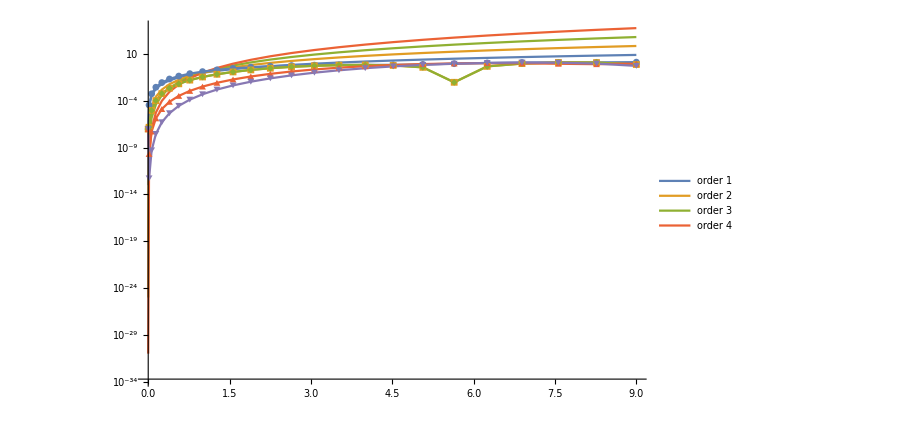

```mathematica
Show[
ListLogPlot[data2,Joined->True,PlotLegends->Placed[("order "<>ToString[#]&/@{1,2,3,4}),Left]],
ListLogPlot[dists,Frame->True,Background->White,Joined->True,PlotMarkers->{Automatic,7},PlotLegends->Placed[("order "<>ToString[#]&/@{1,"2comp","2scb",3,4}),Right],ImageSize->Large]
]
```

```mathematica
n=1; 
dists=
Table[
dham=MatrixExp[-ⅈ t CalcPauliSumMatrix[ham]]//Chop;
mat=IdentityMatrix[Length@dham];
{t,MatrixDist[dham,mat,Range[Length@dham]-1]//First},{t,time}]
```

Table::iterb: Iterator {t,time} does not have appropriate bounds.

Table[dham=Chop[MatrixExp[-ⅈ t CalcPauliSumMatrix[ham]]];mat=IdentityMatrix[Length[dham]];{t,First[MatrixDist[dham,mat,Range[Length[dham]]-1]]},{t,time}]

```mathematica
n=1; 
dists=
Table[
dham=MatrixExp[-ⅈ t CalcPauliSumMatrix[ham]]//Chop;
mat=IdentityMatrix[Length@dham];
{t,MatrixDist[dham,mat,Range[Length@dham]-1]//First},{t,times}]
```

{{0.001,0.00103023},{0.01,0.0103023},{0.1,0.102978},{1,0.985271},{π,1.8237},{2 π,1.75735},{3 π,1.74471},{4 π,1.75043}}

Try different norm, and find the maximum and minimum

```mathematica
NMinimize[]
```

```mathematica
iddist={{0.0001,0.00011372838338780435},{0.018112673611111112,0.018659976311299873},{0.0671673611111111,0.06918413382993309},{0.14726406250000001,0.15157061210523712},{0.25840277777777776,0.2654292679516704},{0.40058350694444445,0.409771295568257},{0.5738062500000001,0.582583062437991},{0.7780710069444444,0.7803039330333509},{1.0133777777777777,0.9972414582525134},{1.2797265625000003,1.2249808856291768},{1.5771173611111111,1.4518770128894054},{1.905550173611111,1.6627516514482292},{2.2650250000000005,1.8389555360372984},{2.655541840277778,1.9269416034158633},{3.0771006944444443,1.8038507004710385},{3.5297015625000006,1.8715315155779269},{4.013344444444445,1.8344406134967317},{4.528029340277778,1.7900597682318162},{5.07375625,1.9246990830422726},{5.65052517361111,1.8611265307877225},{6.25833611111111,1.7532818091410811},{6.897189062499999,1.8476408341068895},{7.567084027777776,1.8470458064609965},{8.268021006944444,1.8178549620587503},{9.,1.8286312799357152}};
```

```mathematica
AppendTo[dists,iddist]
```

{{{0.0001,1.45502×10^-9},{0.0181127,0.000046946},{0.0671674,0.000645378},{0.147264,0.00309846},{0.258403,0.00950863},{0.400584,0.0226954},{0.573806,0.0459958},{0.778071,0.0828754},{1.01338,0.136281},{1.27973,0.207707},{1.57712,0.296027},{1.90555,0.396314},{2.26503,0.499117},{2.65554,0.590912},{3.0771,0.656926},{3.5297,0.687836},{4.01334,0.69176},{4.52803,0.707248},{5.07376,0.789346},{5.65053,0.947893},{6.25834,1.12562},{6.89719,1.25104},{7.56708,1.29311},{8.26802,1.29721},{9.,1.36365}},{{0.0001,2.40626×10^-11},{0.0181127,2.25295×10^-7},{0.0671674,0.0000114888},{0.147264,0.000120919},{0.258403,0.000651365},{0.400584,0.00241197},{0.573806,0.00701156},{0.778071,0.0171687},{1.01338,0.0368938},{1.27973,0.0713471},{1.57712,0.126119},{1.90555,0.20565},{2.26503,0.310694},{2.65554,0.4349},{3.0771,0.561322},{3.5297,0.660266},{4.01334,0.690674},{4.52803,0.607433},{5.07376,0.376086},{5.65053,0.0117143},{6.25834,0.49119},{6.89719,0.964761},{7.56708,1.26506},{8.26802,1.22677},{9.,0.759178}},{{0.0001,2.40626×10^-11},{0.0181127,2.25295×10^-7},{0.0671674,0.0000114888},{0.147264,0.000120919},{0.258403,0.000651365},{0.400584,0.00241197},{0.573806,0.00701156},{0.778071,0.0171687},{1.01338,0.0368938},{1.27973,0.0713471},{1.57712,0.126119},{1.90555,0.20565},{2.26503,0.310694},{2.65554,0.4349},{3.0771,0.561322},{3.5297,0.660266},{4.01334,0.690674},{4.52803,0.607433},{5.07376,0.376086},{5.65053,0.0117143},{6.25834,0.49119},{6.89719,0.964761},{7.56708,1.26506},{8.26802,1.22677},{9.,0.759178}},{{0.0001,2.40249×10^-11},{0.0181127,3.64507×10^-10},{0.0671674,6.8926×10^-8},{0.147264,1.5956×10^-6},{0.258403,0.0000150855},{0.400584,0.0000870072},{0.573806,0.000365377},{0.778071,0.00122967},{1.01338,0.00351152},{1.27973,0.00882026},{1.57712,0.0199482},{1.90555,0.0412437},{2.26503,0.0787071},{2.65554,0.139433},{3.0771,0.230043},{3.5297,0.354081},{4.01334,0.508941},{4.52803,0.683358},{5.07376,0.856152},{5.65053,0.996252},{6.25834,1.06611},{6.89719,1.03605},{7.56708,0.920262},{8.26802,0.830838},{9.,0.938946}},{{0.0001,2.40249×10^-11},{0.0181127,1.01719×10^-12},{0.0671674,7.12904×10^-10},{0.147264,3.60957×10^-8},{0.258403,5.99457×10^-7},{0.400584,5.34898×10^-6},{0.573806,0.0000320705},{0.778071,0.00014555},{1.01338,0.00053742},{1.27973,0.00168962},{1.57712,0.00466476},{1.90555,0.011555},{2.26503,0.0260758},{2.65554,0.0541857},{3.0771,0.104416},{3.5297,0.187298},{4.01334,0.312979},{4.52803,0.486298},{5.07376,0.699734},{5.65053,0.927061},{6.25834,1.12238},{6.89719,1.22759},{7.56708,1.18606},{8.26802,0.958506},{9.,0.54445}},{{0.0001,0.000113728},{0.0181127,0.01866},{0.0671674,0.0691841},{0.147264,0.151571},{0.258403,0.265429},{0.400584,0.409771},{0.573806,0.582583},{0.778071,0.780304},{1.01338,0.997241},{1.27973,1.22498},{1.57712,1.45188},{1.90555,1.66275},{2.26503,1.83896},{2.65554,1.92694},{3.0771,1.80385},{3.5297,1.87153},{4.01334,1.83444},{4.52803,1.79006},{5.07376,1.9247},{5.65053,1.86113},{6.25834,1.75328},{6.89719,1.84764},{7.56708,1.84705},{8.26802,1.81785},{9.,1.82863}}}

```mathematica
ListLogPlot[dists,Frame->True,Background->White,Joined->True,PlotMarkers->{Automatic,7},PlotLegends->Placed[({"order-1","order-2","order-2scb","order-3","order-4","distance with I"}),Right],ImageSize->Large]
```

ListLogPlot::lpn: dists is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

ListLogPlot[dists,Frame→True,Background→GrayLevel[1],Joined→True,PlotMarkers→{Automatic,7},PlotLegends→Placed[{order-1,order-2,order-2scb,order-3,order-4,distance with I},Right],ImageSize→Large]

```mathematica
dists
```

{{{0.0001,1.45502×10^-9},{0.0181127,0.000046946},{0.0671674,0.000645378},{0.147264,0.00309846},{0.258403,0.00950863},{0.400584,0.0226954},{0.573806,0.0459958},{0.778071,0.0828754},{1.01338,0.136281},{1.27973,0.207707},{1.57712,0.296027},{1.90555,0.396314},{2.26503,0.499117},{2.65554,0.590912},{3.0771,0.656926},{3.5297,0.687836},{4.01334,0.69176},{4.52803,0.707248},{5.07376,0.789346},{5.65053,0.947893},{6.25834,1.12562},{6.89719,1.25104},{7.56708,1.29311},{8.26802,1.29721},{9.,1.36365}},{{0.0001,2.40626×10^-11},{0.0181127,2.25295×10^-7},{0.0671674,0.0000114888},{0.147264,0.000120919},{0.258403,0.000651365},{0.400584,0.00241197},{0.573806,0.00701156},{0.778071,0.0171687},{1.01338,0.0368938},{1.27973,0.0713471},{1.57712,0.126119},{1.90555,0.20565},{2.26503,0.310694},{2.65554,0.4349},{3.0771,0.561322},{3.5297,0.660266},{4.01334,0.690674},{4.52803,0.607433},{5.07376,0.376086},{5.65053,0.0117143},{6.25834,0.49119},{6.89719,0.964761},{7.56708,1.26506},{8.26802,1.22677},{9.,0.759178}},{{0.0001,2.40626×10^-11},{0.0181127,2.25295×10^-7},{0.0671674,0.0000114888},{0.147264,0.000120919},{0.258403,0.000651365},{0.400584,0.00241197},{0.573806,0.00701156},{0.778071,0.0171687},{1.01338,0.0368938},{1.27973,0.0713471},{1.57712,0.126119},{1.90555,0.20565},{2.26503,0.310694},{2.65554,0.4349},{3.0771,0.561322},{3.5297,0.660266},{4.01334,0.690674},{4.52803,0.607433},{5.07376,0.376086},{5.65053,0.0117143},{6.25834,0.49119},{6.89719,0.964761},{7.56708,1.26506},{8.26802,1.22677},{9.,0.759178}},{{0.0001,2.40249×10^-11},{0.0181127,3.64507×10^-10},{0.0671674,6.8926×10^-8},{0.147264,1.5956×10^-6},{0.258403,0.0000150855},{0.400584,0.0000870072},{0.573806,0.000365377},{0.778071,0.00122967},{1.01338,0.00351152},{1.27973,0.00882026},{1.57712,0.0199482},{1.90555,0.0412437},{2.26503,0.0787071},{2.65554,0.139433},{3.0771,0.230043},{3.5297,0.354081},{4.01334,0.508941},{4.52803,0.683358},{5.07376,0.856152},{5.65053,0.996252},{6.25834,1.06611},{6.89719,1.03605},{7.56708,0.920262},{8.26802,0.830838},{9.,0.938946}},{{0.0001,2.40249×10^-11},{0.0181127,1.01719×10^-12},{0.0671674,7.12904×10^-10},{0.147264,3.60957×10^-8},{0.258403,5.99457×10^-7},{0.400584,5.34898×10^-6},{0.573806,0.0000320705},{0.778071,0.00014555},{1.01338,0.00053742},{1.27973,0.00168962},{1.57712,0.00466476},{1.90555,0.011555},{2.26503,0.0260758},{2.65554,0.0541857},{3.0771,0.104416},{3.5297,0.187298},{4.01334,0.312979},{4.52803,0.486298},{5.07376,0.699734},{5.65053,0.927061},{6.25834,1.12238},{6.89719,1.22759},{7.56708,1.18606},{8.26802,0.958506},{9.,0.54445}},{{0.0001,0.000113728},{0.0181127,0.01866},{0.0671674,0.0691841},{0.147264,0.151571},{0.258403,0.265429},{0.400584,0.409771},{0.573806,0.582583},{0.778071,0.780304},{1.01338,0.997241},{1.27973,1.22498},{1.57712,1.45188},{1.90555,1.66275},{2.26503,1.83896},{2.65554,1.92694},{3.0771,1.80385},{3.5297,1.87153},{4.01334,1.83444},{4.52803,1.79006},{5.07376,1.9247},{5.65053,1.86113},{6.25834,1.75328},{6.89719,1.84764},{7.56708,1.84705},{8.26802,1.81785},{9.,1.82863}}}